## Useful Integrals for E_p- E_qDistributions

I’m going to try to do some Gaussian-like integrals but with some polynomial functions where the Gaussian “width” normally is. Let’s see if Mathematica can do them symbolically. My bet is a lot of erfs around.

```mathematica
<<Notation`
```

```mathematica
f[x_]:= α + β*x + γ*x^2
```

```mathematica
ingr[x_]:= Exp[-(A-x)^2/f[x]]*Exp[-a*x]
```

```mathematica
Integrate[ingr[x],{x,ϵ,Infinity}, Assumptions -> a>0 && A>0 && α>0 && β==0 &&γ==0 && ϵ> 0]
```

1/2 ⅇ^(1/4 a (-4 A+a α)) √π √α (1+Erf[(2 A-a α-2 ϵ)/(2 √α)])

```mathematica
ingr[5]
```

ⅇ^(-5 a-(-5+A)^2/(α+5 β+25 γ))

```mathematica
γ=0
```

0

```mathematica
a=0
```

0

```mathematica
Integrate[ingr[x],{x,0,Infinity}, Assumptions -> a==0 && A>0 && α>0 && β>0 &&γ==0 && ϵ> 0]
```

Integrate[ⅇ^(-(A-x)^2/(α+x β)),{x,0,∞},Assumptions→A>0&&α>0&&β>0&&ϵ>0]

```mathematica
Integrate[ⅇ^(-(A-x)^2/(α+x β)),{x,0,∞},Assumptions->A>0&&α>0&&β>0&&ϵ>0]
Plot[ingr[x],{x,0,Infinity}, Assumptions -> a==0 && A==5 && α==1 && β==0 &&γ==0]
```

Integrate[ⅇ^(-(A-x)^2/(α+x β)),{x,0,∞},Assumptions→A>0&&α>0&&β>0&&ϵ>0]

Plot::optx: Unknown option Assumptions→A==5&&α==1&&β==0 in Plot[ingr[x],{x,0,∞},Assumptions→a==0&&A==5&&α==1&&β==0&&γ==0].

Plot[ingr[x],{x,0,∞},Assumptions→a==0&&A==5&&α==1&&β==0&&γ==0]

```mathematica
Manipulate[Plot[ingr[x],{x,0,10}],{A,0,5},{a,0,0},{α,1,1},{β,0,0},{γ,0,0}]
```

```mathematica
A=7
```

7

```mathematica
a=0.01
```

0.01

```mathematica
α=1
```

1

```mathematica
β=1
```

1

```mathematica
γ=1
```

1

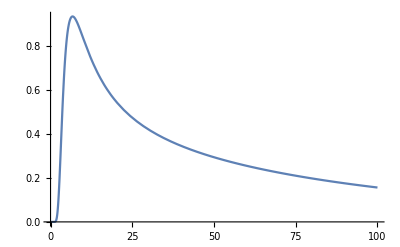

```mathematica
Plot[ingr[x],{x,0,100}]
```

```mathematica
Simplify[Integrate[ingr[x],{x,0,10000000}]]
```

∫_0^10000000 ⅇ^(-0.01 x-(-7+x)^2/(1+x+x^2))ⅆx

```mathematica
NIntegrate[ⅇ^(-0.01 x-(-7+x)^2/(1+x+x^2)),{x,0,10000000}]
```

49.7953

```mathematica
NIntegrate[ⅇ^(-0.01 x-(-7+x)^2/(1+x+x^2)),{x,0,1000000}]
```

49.7953

```mathematica
NIntegrate[ⅇ^(-0.01 x-(-7+x)^2/(1+x+x^2)),{x,0,100}]
```

35.0255